# MacDonald kernel: H-function

## Definition and application

This H function arises for isotropic scattering problems including:

classical exponential random flights in Flatland

BesselK0 random flights in the 1D rod

(2 s BesselK[1,s])/π random flights in 3D

1/2 ⅇ^-s (1+s) random flights in 4D

(2^(1/2-d/2) d s^(1/2 (-1+d)) BesselK[1/2 (-1+d),s])/(√π Gamma[1+d/2]) random flights in dD

## References

Fock, V. 1944. Some integral equations of mathematical physics. In: Doklady AN SSSR, vol.
26, 147–51, http://mi.mathnet.ru/eng/msb6183.

Case, K. M. 1957. On Wiener-Hopf equations. Ann. Phys. (USA) 2(4): 384–405. doi:10. 1016/0003-4916(57)90027-1

Krein, M. G. 1962. Integral equations on a half-line with kernel depending upon the difference of the arguments. Amer. Math. Soc. Transl. 22: 163–288.

Eugene d'Eon & M. M. R. Williams (2018): Isotropic Scattering in a Flatland Half-Space, Journal of Computational and Theoretical Transport, DOI: 10.1080/23324309.2018.1544566

Eugene d’Eon & Norman J. McCormick (2019) Radiative Transfer in Half Spaces of Arbitrary Dimension, Journal of Computational and Theoretical Transport, 48:7, 280-337, DOI: 10.1080/23324309.2019.1696365

## Explicit general solution

The H-function is known explicitly by adapting a derivation of V.A. Fock 1944 [d’Eon and McCormick 2019, Eq.(B.8)].

```mathematica
IFock[x_]:=-2 (x) ArcTanh[ⅇ^(ⅈ (x))]-2 ⅈ PolyLog[2,ⅇ^(ⅈ (x))]+1/2 ⅈ PolyLog[2,ⅇ^(2 ⅈ (x))]
```

```mathematica
MacDonald`H[u_,c_]:= √((1+u)/(1+u √(1-c^2)))Abs[Exp[1/Pi IFock[ArcSec[u]+ArcSin[c]]]]
```

### Identities

A unique identify for the MacDonald kernel is [d’Eon and Williams 2018, Eq.(A.7)]

H(u,c) H(u,-c)==(1+u)/(1+√(1-c^2) u)

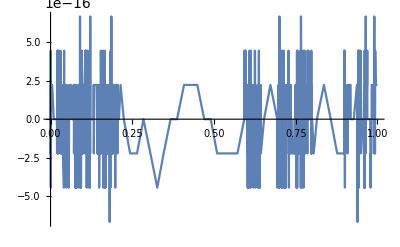

```mathematica
With[{c=0.9},
Plot[{MacDonald`H[u,c]MacDonald`H[u,-c]-((1+u)/(1+√(1-c^2)u))},{u,0,1}]
]
```

### special case c = 1:

[d’Eon and Williams 2018]

```mathematica
MacDonald`Hc1[u_,1]:=√(1+u)Exp[Re[HypergeometricPFQ[{1/2,1,1},{3/2,3/2},1/u^2]/(π u)]]
```

```mathematica
MacDonald`Hc2[u_,1]:=√(1+u)Exp[HypergeometricPFQ[{1/2,1,1},{3/2,3/2},1/u^2]/(π u)+ArcCosh[u]/2]
```

```mathematica
MacDonald`Hc3[u_,1]:=Chop[√(1+u)ⅇ^((ⅈ (PolyLog[2,-(ⅈ (1+√(1-u^2)))/u]-PolyLog[2,(ⅈ (1+√(1-u^2)))/u]))/π) (-ⅈ u-√(1-u^2))^(-ArcSec[u]/π)]
```

```mathematica
N[{MacDonald`Hc1[u,1],MacDonald`Hc1[u,1],MacDonald`Hc1[u,1]}/.u->1/3]
```

{1.55799,1.55799,1.55799}

### special case μ = 1:

[d’Eon and Williams 2018]

```mathematica
MacDonald`Hu1[1,c_]:=√(2/(1+√(1-c^2)))Exp[c/Pi HypergeometricPFQ[{1/2,1,1},{3/2,3/2},c^2]]
```

### Benchmark values

Validated against independent implementation by Barry Ganapol, Dec 2019.

```mathematica
Style[TableForm[
Table[NumberForm[Chop[N[MacDonald`H[u,c],12]],12],{u,1/10,1,1/10},{c,1/10,1,1/10}]
,TableHeadings->{{"μ=0.1","μ=0.2","μ=0.3","μ=0.4","μ=0.5","μ=0.6","μ=0.7","μ=0.8","μ=0.9","μ=1.0"},{"c=0.1","c=0.2","c=0.3","c=0.4","c=0.5","c=0.6","c=0.7","c=0.8","c=0.9","c=1.0"}}],Small]
```

| c=0.1 | c=0.2 | c=0.3 | c=0.4 | c=0.5 | c=0.6 | c=0.7 | c=0.8 | c=0.9 | c=1.0
μ=0.1 | 1.00986237220 | 1.02035969089 | 1.03160591899 | 1.04375534182 | 1.05702663988 | 1.07174978069 | 1.08846994008 | 1.10822822993 | 1.13364867554 | 1.19123896467
μ=0.2 | 1.01545117571 | 1.03214541676 | 1.05032602070 | 1.07032520184 | 1.09261788807 | 1.11792683741 | 1.14745628146 | 1.18352483480 | 1.23202266385 | 1.35300952768
μ=0.3 | 1.01955400755 | 1.04090070058 | 1.06441474026 | 1.09061229185 | 1.12023814909 | 1.15443681754 | 1.19513467971 | 1.24608044459 | 1.31690565057 | 1.50743257854
μ=0.4 | 1.02277520414 | 1.04783494385 | 1.07568183575 | 1.10701407777 | 1.14284807666 | 1.18476064184 | 1.23543325297 | 1.30014319858 | 1.39262299842 | 1.65815909701
μ=0.5 | 1.02539994920 | 1.05352430029 | 1.08499779016 | 1.12069475183 | 1.16189837189 | 1.21061713441 | 1.27030053637 | 1.34781365301 | 1.46125753517 | 1.80666106477
μ=0.6 | 1.02759251403 | 1.05830376879 | 1.09287380232 | 1.13234524502 | 1.17825957533 | 1.23304942534 | 1.30093168779 | 1.39038940537 | 1.52408499104 | 1.95368940562
μ=0.7 | 1.02945790873 | 1.06238935388 | 1.09964260728 | 1.14241993772 | 1.19251069370 | 1.25275993701 | 1.32814219434 | 1.42876717144 | 1.58199073454 | 2.09967931508
μ=0.8 | 1.03106780654 | 1.06592963874 | 1.10553506623 | 1.15123714379 | 1.20506177355 | 1.27025228749 | 1.35252499871 | 1.46360913832 | 1.63563687330 | 2.24490466816
μ=0.9 | 1.03247341547 | 1.06903152309 | 1.11071857647 | 1.15902972215 | 1.21621583758 | 1.28590306999 | 1.37452972786 | 1.49542586127 | 1.68554302220 | 2.38954819078
μ=1.0 | 1.03371259147 | 1.07177452765 | 1.11531854174 | 1.16597352752 | 1.22620388089 | 1.30000256645 | 1.39450766349 | 1.52462299406 | 1.73213062123 | 2.53373727949

### special values

[d’Eon and Williams 2018, Eq.(A.18)]

```mathematica
MacDonald`H[1,1]
```

√2 ⅇ^((2 Catalan)/π)

[d’Eon and McCormick 2019, Eq.(B.13)]

```mathematica
FullSimplify[Log[MacDonald`H[1,1/2]]==Log[2 Exp[4 Catalan / (3 Pi)]/(2+√3)^(2/3)]]
```

True

## Additional representations

### Form 2

[d’Eon and McCormick 2019 - Eq.(B.8)]

```mathematica
MacDonald`H2[u_,c_]:= √((1+u)/(1+u √(1-c^2)))Exp[1/(2Pi)(IFock[ArcSec[u]+ArcSin[c]]-IFock[ArcSec[u]-ArcSin[c]])]
```

```mathematica
Style[TableForm[
Table[NumberForm[Chop[N[MacDonald`H2[u,c],12]],12],{u,1/10,1,1/10},{c,1/10,1,1/10}]
,TableHeadings->{{"μ=0.1","μ=0.2","μ=0.3","μ=0.4","μ=0.5","μ=0.6","μ=0.7","μ=0.8","μ=0.9","μ=1.0"},{"c=0.1","c=0.2","c=0.3","c=0.4","c=0.5","c=0.6","c=0.7","c=0.8","c=0.9","c=1.0"}}],Small]
```

| c=0.1 | c=0.2 | c=0.3 | c=0.4 | c=0.5 | c=0.6 | c=0.7 | c=0.8 | c=0.9 | c=1.0
μ=0.1 | 1.00986237220 | 1.02035969089 | 1.03160591899 | 1.04375534182 | 1.05702663988 | 1.07174978069 | 1.08846994008 | 1.10822822993 | 1.13364867554 | 1.19123896467
μ=0.2 | 1.01545117571 | 1.03214541676 | 1.05032602070 | 1.07032520184 | 1.09261788807 | 1.11792683741 | 1.14745628146 | 1.18352483480 | 1.23202266385 | 1.35300952768
μ=0.3 | 1.01955400755 | 1.04090070058 | 1.06441474026 | 1.09061229185 | 1.12023814909 | 1.15443681754 | 1.19513467971 | 1.24608044459 | 1.31690565057 | 1.50743257854
μ=0.4 | 1.02277520414 | 1.04783494385 | 1.07568183575 | 1.10701407777 | 1.14284807666 | 1.18476064184 | 1.23543325297 | 1.30014319858 | 1.39262299842 | 1.65815909701
μ=0.5 | 1.02539994920 | 1.05352430029 | 1.08499779016 | 1.12069475183 | 1.16189837189 | 1.21061713441 | 1.27030053637 | 1.34781365301 | 1.46125753517 | 1.80666106477
μ=0.6 | 1.02759251403 | 1.05830376879 | 1.09287380232 | 1.13234524502 | 1.17825957533 | 1.23304942534 | 1.30093168779 | 1.39038940537 | 1.52408499104 | 1.95368940562
μ=0.7 | 1.02945790873 | 1.06238935388 | 1.09964260728 | 1.14241993772 | 1.19251069370 | 1.25275993701 | 1.32814219434 | 1.42876717144 | 1.58199073454 | 2.09967931508
μ=0.8 | 1.03106780654 | 1.06592963874 | 1.10553506623 | 1.15123714379 | 1.20506177355 | 1.27025228749 | 1.35252499871 | 1.46360913832 | 1.63563687330 | 2.24490466816
μ=0.9 | 1.03247341547 | 1.06903152309 | 1.11071857647 | 1.15902972215 | 1.21621583758 | 1.28590306999 | 1.37452972786 | 1.49542586127 | 1.68554302220 | 2.38954819078
μ=1.0 | 1.03371259147 | 1.07177452765 | 1.11531854174 | 1.16597352752 | 1.22620388089 | 1.30000256645 | 1.39450766349 | 1.52462299406 | 1.73213062123 | 2.53373727949

### Form 3

```mathematica
Sum[(√π Gamma[(1+j)/2])/(j^2 Gamma[j/2])Sin[y]^j,{j,1,Infinity,2}]
```

HypergeometricPFQ[{1/2,1,1},{3/2,3/2},Sin[y]^2] Sin[y]

```mathematica
D[HypergeometricPFQ[{1/2,1,1},{3/2,3/2},x^2] x,x]//FullSimplify
```

ArcSin[x]/(x √(1-x^2))

```mathematica
Sum[(√π Gamma[(1+j)/2])/(j^1 Gamma[j/2])x^(j-1),{j,1,Infinity,2}]
```

ArcSin[x]/(x √(1-x^2))

```mathematica
MacDonald`Χ[y_]:=Re[HypergeometricPFQ[{1/2,1,1},{3/2,3/2},Sin[y]^2] Sin[y]]
```

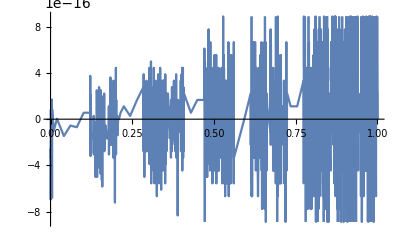

```mathematica
Plot[Re[IFock[x]]-MacDonald`Χ[x],{x,0,1}]
```

```mathematica
MacDonald`H3[u_,c_]:= √((1+u)/(1+u √(1-c^2)))Exp[1/(2Pi)(MacDonald`Χ[ArcSec[u]+ArcSin[c]]-MacDonald`Χ[ArcSec[u]-ArcSin[c]])]
```

```mathematica
MacDonald`H3[1,1/2]//FullSimplify
```

(2 ⅇ^((4 Catalan)/(3 π)))/(2+√3)^(2/3)

```mathematica
Style[TableForm[
Table[NumberForm[Chop[N[MacDonald`H3[u,c],12]],12],{u,1/10,1,1/10},{c,1/10,1,1/10}]
,TableHeadings->{{"μ=0.1","μ=0.2","μ=0.3","μ=0.4","μ=0.5","μ=0.6","μ=0.7","μ=0.8","μ=0.9","μ=1.0"},{"c=0.1","c=0.2","c=0.3","c=0.4","c=0.5","c=0.6","c=0.7","c=0.8","c=0.9","c=1.0"}}],Small]
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating HypergeometricPFQ[{1/2,1,1},{3/2,3/2},Sin[ArcSec[4/5]+ArcSin[7/10]]^2].

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating HypergeometricPFQ[{1/2,1,1},{3/2,3/2},Sin[ArcSec[4/5]-ArcSin[7/10]]^2].

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating HypergeometricPFQ[{1/2,1,1},{3/2,3/2},Sin[ArcSec[9/10]+ArcSin[9/10]]^2].

General::stop: Further output of N::meprec will be suppressed during this calculation.

| c=0.1 | c=0.2 | c=0.3 | c=0.4 | c=0.5 | c=0.6 | c=0.7 | c=0.8 | c=0.9 | c=1.0
μ=0.1 | 1.00986237220 | 1.02035969089 | 1.03160591899 | 1.04375534182 | 1.05702663988 | 1.07174978069 | 1.08846994008 | 1.10822822993 | 1.13364867554 | 1.19123896467
μ=0.2 | 1.01545117571 | 1.03214541676 | 1.05032602070 | 1.07032520184 | 1.09261788807 | 1.11792683741 | 1.14745628146 | 1.18352483480 | 1.23202266385 | 1.35300952768
μ=0.3 | 1.01955400755 | 1.04090070058 | 1.06441474026 | 1.09061229185 | 1.12023814909 | 1.15443681754 | 1.19513467971 | 1.24608044459 | 1.31690565057 | 1.50743257854
μ=0.4 | 1.02277520414 | 1.04783494385 | 1.07568183575 | 1.10701407777 | 1.14284807666 | 1.18476064184 | 1.23543325297 | 1.30014319858 | 1.39262299842 | 1.65815909701
μ=0.5 | 1.02539994920 | 1.05352430029 | 1.08499779016 | 1.12069475183 | 1.16189837189 | 1.21061713441 | 1.27030053637 | 1.34781365301 | 1.46125753517 | 1.80666106477
μ=0.6 | 1.02759251403 | 1.05830376879 | 1.09287380232 | 1.13234524502 | 1.17825957533 | 1.23304942534 | 1.30093168779 | 1.39038940537 | 1.52408499104 | 1.95368940562
μ=0.7 | 1.02945790873 | 1.06238935388 | 1.09964260728 | 1.14241993772 | 1.19251069370 | 1.25275993701 | 1.32814219434 | 1.42876717144 | 1.58199073454 | 2.09967931508
μ=0.8 | 1.03106780654 | 1.06592963874 | 1.10553506623 | 1.15123714379 | 1.20506177355 | 1.27025228749 | 1.35252499871 | 1.46360913832 | 1.63563687330 | 2.24490466816
μ=0.9 | 1.03247341547 | 1.06903152309 | 1.11071857647 | 1.15902972215 | 1.21621583758 | 1.28590306999 | 1.37452972786 | 1.49542586127 | 1.68554302220 | 2.38954819078
μ=1.0 | 1.03371259147 | 1.07177452765 | 1.11531854174 | 1.16597352752 | 1.22620388089 | 1.30000256645 | 1.39450766349 | 1.52462299406 | 1.73213062123 | 2.53373727949

### Form 4

```mathematica
MacDonald`H4[u_,c_]:= √((1+u)/(1+u √(1-c^2)))Exp[1/Pi Re[HypergeometricPFQ[{1/2,1,1},{3/2,3/2},Sin[#]^2] Sin[#]&[ArcSec[u]+ArcSin[c]]]]
```

### Form 5

```mathematica
Leftover[x_]:=+ⅈ (PolyLog[2,-ⅇ^(ⅈ x)]-PolyLog[2,ⅇ^(ⅈ x)])
```

```mathematica
MacDonald`H5[u_,c_]:= √((1+u)/(1+u √(1-c^2)))Abs[
((1-ⅇ^(ⅈ (ArcSec[u]+ArcSin[c])))^(ArcSec[u]+ArcSin[c]) (1+ⅇ^(ⅈ (ArcSec[u]+ArcSin[c])))^(-ArcSec[u]-ArcSin[c]))^(1/Pi)
Exp[1/Pi Leftover[ArcSec[u]+ArcSin[c]]]
]
```

```mathematica
MacDonald`H5[1,1/2]==MacDonald`H[1,1/2]//FullSimplify
```

True

### Expansion of Fock’s integral

```mathematica
Integrate[x/Sin[x],x]
```

x (Log[1-ⅇ^(ⅈ x)]-Log[1+ⅇ^(ⅈ x)])+ⅈ (PolyLog[2,-ⅇ^(ⅈ x)]-PolyLog[2,ⅇ^(ⅈ x)])

```mathematica
IFocksum[x_,J_]:=Sum[-((ⅈ^j (-2+2^j) BernoulliB[j]) x^(j+1))/(j! (j+1)),{j,0,J,2}]
```

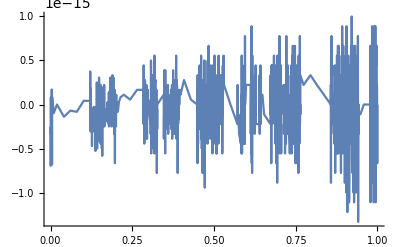

```mathematica
Plot[{Re[IFock[x]]-Re[IFocksum[x,50]]},{x,0,1},PlotRange->All]
```

```mathematica
IFocksum[x,15]
```

x+x^3/18+(7 x^5)/1800+(31 x^7)/105840+(127 x^9)/5443200+(73 x^11)/37635840+(1414477 x^13)/8499883392000+(8191 x^15)/560431872000

```mathematica
Series[x (Log[1-ⅇ^(ⅈ x)]-Log[1+ⅇ^(ⅈ x)])+ⅈ (PolyLog[2,-ⅇ^(ⅈ x)]-PolyLog[2,ⅇ^(ⅈ x)]),{x,0,15},Assumptions->0<x<1]
```

-(ⅈ π^2)/4+x+x^3/18+(7 x^5)/1800+(31 x^7)/105840+(127 x^9)/5443200+(73 x^11)/37635840+(1414477 x^13)/8499883392000+(8191 x^15)/560431872000+O[x]^16

### Numerical Integration - Form 1

```mathematica
MacDonald`NH1[u_,c_]:=(1+u)/(1+√(1-c^2)u)Exp[NIntegrate[c/Pi(t ArcTan[u t])/((t^2+1)(c+√(t^2+1))),{t,0,Infinity}]]
```

```mathematica
MacDonald`NH1b[u_,c_]:=Exp[NIntegrate[c/Pi(t ArcTan[u t])/((t^2+1)(-c+√(t^2+1))),{t,0,Infinity}]]
```

```mathematica
MacDonald`NH1c[u_,c_]:=√((1+u)/(1+√(1-c^2)u))Exp[NIntegrate[c/Pi(t ArcTan[t u])/(√(1+t^2) (1-c^2+t^2)),{t,0,Infinity}]]
```

```mathematica
MacDonald`NH1c[u_,c_,J_]:=√((1+u)/(1+√(1-c^2)u))Exp[Sum[(c^j Gamma[(1+j)/2] Hypergeometric2F1Regularized[1,(1+j)/2,(2+j)/2,1-1/u^2])/(2 j √π u),{j,1,J-1,2}]+NIntegrate[(c^J t ArcTan[t u])/((1+t^2)^(J/2) (π-c^2 π+π t^2)),{t,0,Infinity}]]
```

```mathematica
MacDonald`NH1c[u_,c_,3]:=√((1+u)/(1+√(1-c^2)u))Exp[Chop[(c ArcSin[√#1])/(π u √(-(-1+#1) #1))]&[1-1/u^2]+NIntegrate[(c^3 t ArcTan[t u])/((1+t^2)^(3/2) (π-c^2 π+π t^2)),{t,0,Infinity}]]
```

```mathematica
MacDonald`NH1c[u_,c_,5]:=√((1+u)/(1+√(1-c^2)u))Exp[Chop[(-c^3 √(-(-1+#1) #1)+c ArcSin[√#1] (c^2+3 #1))/(3 π u √(1-#1) #1^(3/2))]&[1-1/u^2]+NIntegrate[(c^5 t ArcTan[t u])/((1+t^2)^(5/2) (π-c^2 π+π t^2)),{t,0,Infinity}]]
```

```mathematica
MacDonald`NH1c[u_,c_,7]:=√((1+u)/(1+√(1-c^2)u))Exp[Chop[(c ArcSin[√#1] (3 c^4+5 c^2 #1+15 #1^2)-c^3 ((5+2 c^2) √(1-#1) #1^(3/2)+3 c^2 √(-(-1+#1) #1)))/(15 π u √(1-#1) #1^(5/2))]&[1-1/u^2]+NIntegrate[(c^7 t ArcTan[t u])/((1+t^2)^(7/2) (π-c^2 π+π t^2)),{t,0,Infinity}]]
```

```mathematica
MacDonald`NH1d[u_,c_,J_]:=√((1+u)/(1+√(1-c^2)u))Exp[Sum[(c^j Gamma[(1+j)/2] Hypergeometric2F1Regularized[1,(1+j)/2,(2+j)/2,1-1/u^2])/(2 j √π u),{j,1,J-1,2}]+NIntegrate[(c^J t ArcTan[t u])/((1+t^2)^(J/2) (π-c^2 π+π t^2)),{t,0,Infinity}]]
```

```mathematica
N[{MacDonald`H[7/10,9/10],MacDonald`NH1[7/10,9/10],MacDonald`NH1b[7/10,9/10],MacDonald`NH1c[7/10,9/10],MacDonald`NH1c[7/10,9/10,10]}]
```

{1.58199,1.58199,1.58199,1.58199,1.5848}

### Numerical Integration - Form 2

```mathematica
MacDonald`NH2f[u_,c_]:=(1+u)/(1+√(1-c^2)u)Exp[-u/Pi NIntegrate[Log[(1-c/(√(1+t^2)))(t^2+1)/(t^2+1-c^2)]/(1+t^2 u^2),{t,0,Infinity}]]
```

```mathematica
MacDonald`NH2[u_,c_]:=(1+u)/(1+√(1-c^2)u)Exp[NIntegrate[u/Pi Log[1+c/(√(1+t^2))]/(1+t^2 u^2),{t,0,Infinity}]]
```

```mathematica
MacDonald`NH2b[u_,c_]:=Exp[NIntegrate[-u/Pi Log[1-c/(√(1+t^2))]/(1+t^2 u^2),{t,0,Infinity}]]
```

```mathematica
MacDonald`NH2c[u_,c_,J_]:=√((1+u)/(1+√(1-c^2)u))Exp[Sum[(c^j Gamma[(1+j)/2] Hypergeometric2F1Regularized[1,(1+j)/2,(2+j)/2,1-1/u^2])/(2 j √π u),{j,1,J-1,2}]+NIntegrate[u/Pi(((-1)^(1+J) c^J (1+t^2)^(-J/2) Hypergeometric2F1[1,J/2,1+J/2,c^2/(1+t^2)])/J)/(1+t^2 u^2),{t,0,Infinity}]]
```

```mathematica
N[{MacDonald`H[7/10,9/10],MacDonald`NH2f[7/10,9/10],MacDonald`NH2[7/10,9/10],MacDonald`NH2b[7/10,9/10],MacDonald`NH2c[7/10,9/10,100]}]
```

{1.58199,1.58199,1.58199,1.58199,1.58199}

### Numerical Integration - Form 3

```mathematica
MacDonald`NH3[u_,c_]:=(1+u)/(1+√(1-c^2)u)Exp[NIntegrate[1/Pi(u y Log[1+c/y])/(√(-1+y^2) (1+u^2 (-1+y^2))),{y,1,Infinity}]]
```

```mathematica
MacDonald`NH3b[u_,c_]:=Exp[NIntegrate[-u/Pi(y Log[1-c/y])/(√(-1+y^2) (1+u^2 (-1+y^2))),{y,1,Infinity}]]
```

```mathematica
MacDonald`NH3c[u_,c_]:=√((1+u)/(1+√(1-c^2)u))Exp[NIntegrate[(u y ArcTanh[c/y])/(π √(-1+y^2) (1-u^2+u^2 y^2)),{y,1,Infinity}]]
```

```mathematica
N[{MacDonald`H[7/10,9/10],MacDonald`NH3[7/10,9/10],MacDonald`NH3b[7/10,9/10],MacDonald`NH3c[7/10,9/10]}]
```

{1.58199,1.58199,1.58199,1.58199}

### Numerical Integration - Form 4

```mathematica
MacDonald`NH4[u_,c_]:=(1+u)/(1+√(1-c^2)u)Exp[NIntegrate[(u Csc[x]^2 Log[1+c Sin[x]])/(π+π u^2 Cot[x]^2),{x,0,Pi/2}]]
```

```mathematica
MacDonald`NH4o[u_,c_]:=(1+u)/(1+√(1-c^2)u)Exp[NIntegrate[u/Pi Log[1+c Sin[x]]/(u^2 Cos[x]^2+Sin[x]^2),{x,0,Pi/2}]]
```

```mathematica
MacDonald`NH4oo[u_,c_]:=(1+u)/(1+√(1-c^2)u)Exp[u/Pi(1/2 π √(1/u^2) Log[1+c]-NIntegrate[(c ArcCot[u Cot[x]] Cos[x])/(u+c u Sin[x]),{x,0,Pi/2}])];
```

```mathematica
MacDonald`NH4oo2[u_,c_]:=((1+u)√(1+c))/(1+√(1-c^2)u)Exp[-u/Pi(NIntegrate[(c ArcCot[u Cot[x]] Cos[x])/(u+c u Sin[x]),{x,0,Pi/2}])];
```

```mathematica
MacDonald`NH4oo3[u_,c_]:=Exp[-u/Pi(1/2 π √(1/u^2) Log[1-c]-NIntegrate[(-c ArcCot[u Cot[x]] Cos[x])/(u-c u Sin[x]),{x,0,Pi/2}])];
```

```mathematica
MacDonald`NH4oo4[u_,c_]:=(√(1-c))^-1 Exp[u/Pi(NIntegrate[(-c ArcCot[u Cot[x]] Cos[x])/(u-c u Sin[x]),{x,0,Pi/2}])];
```

```mathematica
MacDonald`NH4oo5[u_,c_]:=Chop[((1+u)√(1+c))/(1+√(1-c^2)u)Exp[-u/Pi(NIntegrate[-(c^2 ArcCot[u Cot[x]] Cos[x])/(c u+u Csc[x]),{x,0,Pi/2}])-(c (π+(2 ⅈ u ArcSec[u])/(√(1-u^2))))/(2 π)]];
```

```mathematica
MacDonald`NH4b[u_,c_]:=Exp[NIntegrate[(-u Csc[x]^2 Log[1-c Sin[x]])/(π+π u^2 Cot[x]^2),{x,0,Pi/2}]]
```

```mathematica
MacDonald`NH4c[u_,c_]:=√((1+u)/(1+√(1-c^2)u))Exp[NIntegrate[(u ArcTanh[c Sin[x]] Csc[x]^2)/(π (1+u^2 Cot[x]^2)),{x,0,Pi/2}]]
```

```mathematica
MacDonald`NH4c[u_,c_,J_]:=√((1+u)/(1+√(1-c^2)u))Exp[Sum[(c^j Gamma[(1+j)/2] Hypergeometric2F1Regularized[1,(1+j)/2,(2+j)/2,1-1/u^2])/(2 j √π u),{j,1,J-1,2}]+NIntegrate[((-1)^J c^J u Csc[x]^2 Hypergeometric2F1[1,J/2,1+J/2,c^2 Sin[x]^2] (-Sin[x])^J)/(J π (1+u^2 Cot[x]^2)),{x,0,Pi/2}]]
```

```mathematica
N[{MacDonald`H[7/10,9/10],MacDonald`NH4[7/10,9/10],MacDonald`NH4o[7/10,9/10],MacDonald`NH4oo[7/10,9/10],MacDonald`NH4oo2[7/10,9/10],MacDonald`NH4oo2[7/10,9/10],MacDonald`NH4oo3[7/10,9/10],MacDonald`NH4oo4[7/10,9/10],MacDonald`NH4oo5[7/10,9/10],MacDonald`NH4b[7/10,9/10],MacDonald`NH4c[7/10,9/10],MacDonald`NH4c[7/10,9/10,11]}]
```

{1.58199,1.58199,1.58199,1.58199,1.58199,1.58199,1.58199,1.58199,1.58199,1.58199,1.58199,1.58199}

### Numerical Integration - Form 5

```mathematica
MacDonald`NH5c[u_,c_]:=√((1+u)/(1+√(1-c^2)u))Exp[NIntegrate[(c^2 u ArcTanh[y])/(π √((c-y) (c+y)) (y^2+u^2 (c-y) (c+y))),{y,0,c}]]
```

```mathematica
N[{MacDonald`H[7/10,9/10],MacDonald`NH5c[7/10,9/10]}]
```

{1.58199,1.58199}

### Numerical Integration - Form 6

```mathematica
MacDonald`NH6c[u_,c_]:=√((1+u)/(1+√(1-c^2)u))Exp[NIntegrate[(c^2 u ArcTanh[√(c^2-Y^2)])/(π Y (c^2+(-1+u^2) Y^2))(Y/(√(c^2-Y^2))),{Y,0,c}]]
```

```mathematica
N[{MacDonald`H[7/10,9/10],MacDonald`NH6c[7/10,9/10]}]
```

{1.58199,1.58199}

### Numerical Integration - Fox / Mullikin / Case & Zweifel forms

```mathematica
MacDonald`HFox[u_,c_]:=(√(1+c) (1+u))/(1+√(1-c^2) u)Exp[-1/Pi NIntegrate[ArcTan[(c t)/(√(1-t^2))]/(t+u),{t,0,1}]]
```

```mathematica
MacDonald`HMullikin54[u_,c_]:=(1+u)/(1+√(1-c^2)u) Exp[u/Pi NIntegrate[ArcTan[(c t)/(√(1-t^2))]/(t(t+u)),{t,0,1}]]
```

CaseZw67: integration by parts p.130

```mathematica
MacDonald`HCZ1[u_,c_]:=(√(1+c) (1+u))/(1+√(1-c^2) u)Exp[-1/Pi(Log[1+u] Pi/2-NIntegrate[Log[t+u] c/(√(1-t^2) (1+(-1+c^2) t^2)),{t,0,1}])]
```

```mathematica
MacDonald`HCZ2[u_,c_]:=(√(1+c) √(1+u))/(1+√(1-c^2) u)Exp[1/Pi(NIntegrate[Log[t+u] c/(√(1-t^2) (1+(-1+c^2) t^2)),{t,0,1}])]
```

```mathematica
N[{MacDonald`H[7/10,9/10],MacDonald`HFox[7/10,9/10],MacDonald`HMullikin54[7/10,9/10],MacDonald`HCZ1[7/10,9/10],MacDonald`HCZ2[7/10,9/10]}]
```

{1.58199,1.58199,1.58199,1.58199,1.58199}